## TTM4185 Øving 4: Topologier

Oppgave sist oppdatert: November 2019, Eivind Høydal (Vit.ass) - endret fomulering av oppgave III.2(c) og III.3(a).

(utviklet av  Poul E. Heegaard og Jonas Wäfler, PhD, nå Powel)

## Formål

- Vise ulike strukturer
	- Ring (to enveis-linker, toveis-linker)
	- Stjerne
	- Grid (maske)
	- Kombinert/reelt nettdesign: grid kjerne + ring edge/metro + stjerne aksess
	- Tilfeldige grafer med ulike egenskaper (som skal representere reelle nett og sammensatte nett, dvs. Internett)
- Karakterisere strukturer 
	- Nodegrad (antall linker per node, gjennomsnitt og fordeling)
	- Fjerne linker (linkfeil) tilfeldig og målrettet, fra ulike strukturer og studere når grafen “bryter sammen”, dvs. hvor mange linker (forventet) som må fjernes før nettet betraktes som ubrukelig.

## How to

Mathematica jobber med celler (visualisert med en parantes på høyre side). Du kan åpne/lukke en celle ved å dobbelklikke på parantesen. En lukket celle har en liten pil nederst.

I et felt som er gult trenger du ikke å skrive noe, du må bare kjøre koden som står der. Det gjør du ved først å trykke på feltet, for så å trykke inn SHIFT og ENTER samtidig. Det er nødvendig at du kjører de gule feltene, de genererer variabler og objekter som brukes i andre oppgaver.

Felt som er røde er input-felt, her skal du besvare spørsmål med enten tekst eller kode.

Du skal kun levere den utfylte Mathematica-filen (ingen egen rapport)

I del 1 settes nettverket opp og det er noen innledende oppgaver. Mesteparten av oppgavene til Hovedsakelig er det i del 2 og 3 studenten sk

Del I setter opp nettverk og har et få tasks (røde felt), de fleste tasks er i Del II og Del III.

## DEL I: Plott ulike strukturer

I første delen lager vi alle nettverk. I de første tre oppgavene lages nettverk som består av ring-, grid- og tre-strukturer. I oppgave 1.4 lager vi random-grafer.

### Noen nyttige mathematica-funksjoner

Mathematica har mange nyttige funksjoner for å analysere grafer:

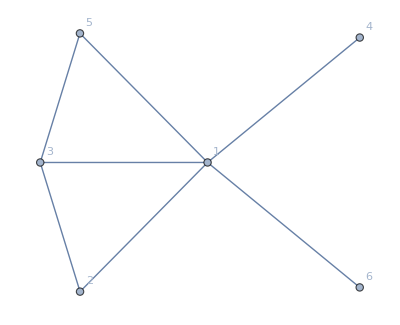

^3

```mathematica
(* create another graph with undirectional edges *)
(* define set of nodes/vertices *)
vExample2 ={1,2,3,4,5,6};
(* define set of undirectional edges *)
eExample2 = {1<->2,1<->3,1<->4,1<->5,2<->3,3<->5,1<->6};
TestGraph2=Graph[vExample2,eExample2,
VertexLabels->"Name"]
```

Få liste over noder og kanter i en graf:

```mathematica
VertexList[TestGraph2]
EdgeList[TestGraph2]

(* Antall noder og lenker i graf *)
VertexList[TestGraph2]//Length
EdgeList[TestGraph2]//Length
```

{1,2,3,4,5,6}

{1<->2,1<->3,1<->4,1<->5,2<->3,3<->5,1<->6}

6

7

VertexDegree gir en liste med antall linker per node. Dvs. første tall i output er antall linker til node 1, andre tall antall linker til node 2 osv.

```mathematica
VertexDegree[TestGraph2]
```

{5,2,3,1,2,1}

Med funksjonen Histogram kan distribusjonen til nodene genereres (fordeling av antall kanter til nodene).
Histogram teller hvor mange ganger de forskjellige verdier er tilstede. X-aksen viser verdi og y-akse antall noder med denne verdi.

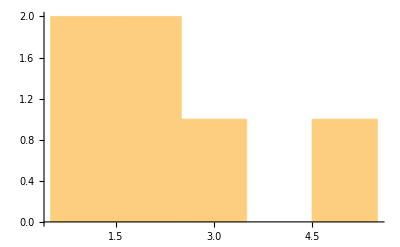

```mathematica
Histogram[VertexDegree[TestGraph2], 10]
(* andre input-parameter (10) sier hvor mange "bins" histogram skal bruke. Du kan forandre verdien (sett den til f.eks. 2) og prøv å forstå hva som skjer *)
```

```mathematica
?FindShortestPath
```

```mathematica
?VertexDelete
```

```mathematica
?HighlightGraph
```

### Oppgave I.1 Plott en ringstruktur med 50 noder

En ringstruktur finner man blant annet i optiske fiberringer (i kjernenettet) som realiserer Sonet/SDH.  
Disse ringene har gjerne to senderetninger slik at en node i kan sende både til node i+1 og node i-1.

En typisk topologi er for eksempel en ringstruktur. En slik topologi vil ha en primærring og en sekudærring, som brukes til backup hvis det oppstår feil.
Primær- og sekundærringen vil ha hver sin senderetning.  Dvs. at primærringen sender fra node i-1→  node i → node i+1→..., mens sekundærringen sender fra node i+1→ i → i-1→...
Ringstrukturer (fysiske/logiske) finnes også i kantnett/metronett hvor mange kunder blir berørt av en feil slik at redundans betaler seg. 

Toveisringer kan illustreres som en ring med urettede kanter (begge retninger er tillatt), eller to ringer med rettede kanter (bare én retning er tillatt).

Pålitelighet:
Med feil i én node vil ringene bli åpnet, men det finnes fortsatt en rute mellom to tilfeldig valgte noder (det forutsetter at en switchover i nodene er mulig slik at “motsatt vei” via sekundærringen kan benyttes, dvs. routingtabellen må oppdateres).
Hvis en link feiler så vil ringen forstatt være fullt sammenkoblet.  
Alle doble feil vil dele/partisjonere ringen i to halvdeler som hver for seg er fullt sammenkoblet.

Vi gir først et eksempel som viser hvordan en graf kan lages:

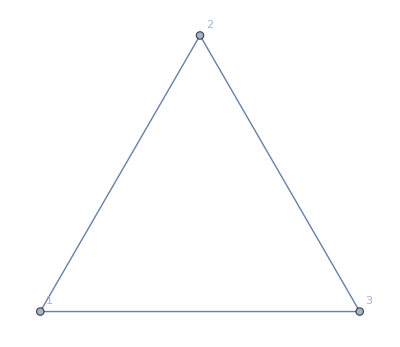

```mathematica
(* create fully connected graph with 3 nodes, with undirectional edges *)
(* define set of nodes/vertices *)
vExample ={1,2,3};
(* define set of undirectional edges *)
eExampleUndirectional = {1<->2,1<->3,2<->3};
(* create the graph *)
Graph[vExample,eExampleUndirectional,
VertexLabels->"Name"]
```

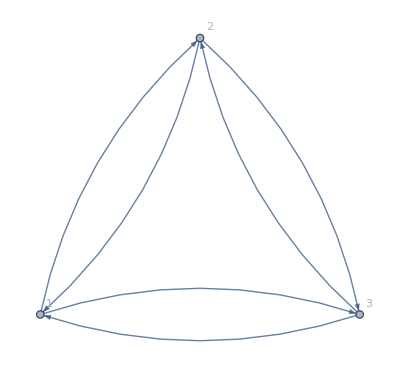

```mathematica
(* create fully connected graph with 3 nodes, with undirectional edges *)
(* define set of directional edges *)
eExampleDirectional = {1->2,2->1,1->3,3->1,2->3,3->2};
(* create the graph *)
Graph[vExample,eExampleDirectional,
VertexLabels->"Name"]
```

For større grafer er det mye lettere å lage kant- og nodelister automatisk med “Table”-kommandoen.

#### Plott en graf med 50 noder ved bruk av toveis-linker

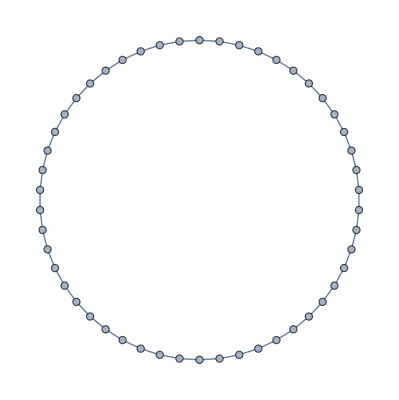

```mathematica
(* Ring with undirectional links *)
Subscript[V, R] =Table[i,{i,50}];
Subscript[E, R] = Table[i<-> Mod[i,50]+1,{i,1,50}];
Subscript[G, R]= Graph[Subscript[V, R],Subscript[E, R]]
```

#### Plott en graf med 50 noder ved bruk av enveis-linker (directional links med primær- og sekundærring)

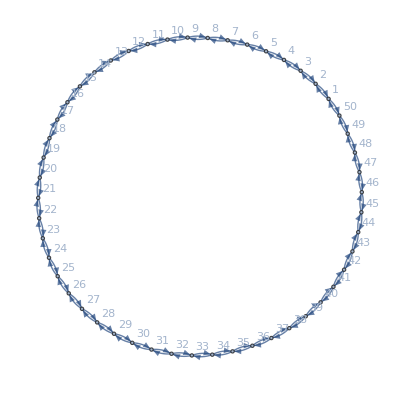

```mathematica
(* Ring with directional links *)
Subscript[V, R] =Table[i,{i,50}];
Subscript[LE, R] = Table[i->  Mod[i,50]+1,{i,1,50}];
Subscript[RE, R] = Table[ Mod[i,50]+1-> i,{i,1,50}];
Subscript[DE, R]=Flatten[{Subscript[LE, R],Subscript[RE, R]}];
Subscript[G, VR]= Graph[Subscript[V, R],Subscript[DE, R],
VertexLabels->"Name"]

(* Function for creation of ring topology with m-(n+1) nodes, undirectional (or bidirectional) links, numbered from n to m and in additon node s*)
Subscript[FE, R][s_,n_,m_]:=Flatten[{{s<->n},Table[i<-> i+1,{i,n,m-1}],{m<-> s}}];
(* sample code: 
Subscript[FE, R][1,9,10]
Graph[Flatten[{1,Range[9,10]}],Subscript[FE, R][1,9,10],
VertexLabels->"Name"]
*)
```

#### (a) Hva er korteste vei mellom node 1 og 20 før og etter at node 10 har feilet? Forklar hva som skal til for å få optimal ruting (korteste vei) etter en nodefeil. Hvor mange og hvilke noder må feile for at veien mellom node 1 og 20 blir avbrutt? Blir svaret annerledes hvis vi ser på en graf med toveis-linker?

Hint: Bruk FindShortestPath og VertexDelete

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

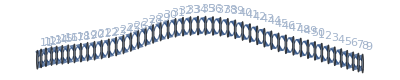

{1,50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20}

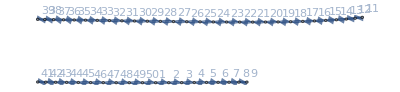

IngenVei:{}

```mathematica
(* your code *)
FindShortestPath[Subscript[G, VR], 1, 20]
Subscript[G, VR] = VertexDelete[Subscript[G, VR], 10]
FindShortestPath[Subscript[G, VR], 1, 20]
Subscript[G, VR] = VertexDelete[Subscript[G, VR], 40]
IngenVei: FindShortestPath[Subscript[G, VR], 1, 20]
```

svar:
(* Hva er korteste vei mellom node 1 og 20 før og etter at node 10 har feilet? *)
Før:
{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

Etter:
{1,50,49,48,47,46,45,44,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,22,21,20}


(* Forklar hva som skal til for å få optimal ruting (korteste vei) etter en nodefeil. *)
En mulighet er at alle nodene er koblet til hverandre, - alle-til-alle. Kan også vurdere å endre routing-tabell.

(* Hvor mange og hvilke noder må feile for at veien mellom node 1 og 20 blir avbrutt? *)
To noder må feile, - én foran startnode, og én etter startnoden. Da kommer den seg ingen vei.


(* Blir svaret annerledes hvis vi ser på en graf med toveis-linker? *)
Nei.

### Oppgave I.2 Plott en grid-struktur (maskenett) med toveis-linker

Grid er en struktur hvor hver node er koblet til naboer i hver dimensjon. 
En endimensjonal grid er en kjede, som danner en ring når endepunktene i kjeden er definert som naboer.
I en todimensjonal grid vil hver node ha fire naboer.  Hvis alle nodene i nettet (inklusive randnoder) har fire naboer så dannes en struktur som kalles en torus (ser ut som en smultring).
Men, i et realistisk (wide area) nett er det ikke naturlig at nodene “langs kanten” vil ha kobling til noder på motsatt side (geografisk avstand er lang og det blir en uøkonomisk løsning).

Eksempel: I denne oppgaven antar vi en todimensjonal grid med 7 noder langs begge dimensjoner.  Nodene numereres slik at Node 1 er koblet til 2 og 8, Node 2 til 1, 3, og 9, Node 3 til 2, 4 og 10, osv. 

Et maskenett (gridstruktur) kan realiseres fysisk (men svært kostbart) eller logisk ved bruk av f.eks. MPLS (hva er MPLS?).  
Som dere vil se når dere plotter koden under så har det en regulær struktur med mange alternative veier mellom nodene.  I et virkelig nett er det sjelden slike regulære strukturer, eller komplette maskenett, men i kjernenettet (over f.eks. optiske ring som nevnt over, eller over et fysisk (delvis)maskenett) er det typisk med mange alternative fysiske veier i et delvis maskenett.

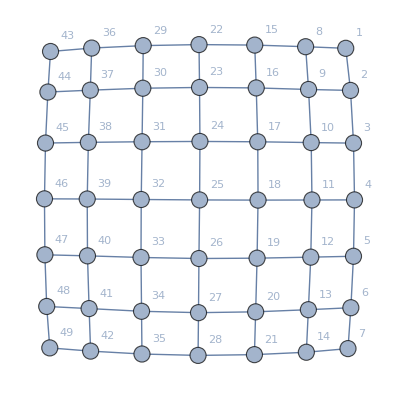

```mathematica
(* Plot 2-dimensjonal grid - maskenett *)
Subscript[V, G]=Table[i,{i,49}];
Subscript[L, G]=Flatten[{Table[{i+j*7<-> i+1+j*7},{i,1,6},{j,0,6}],Table[{i<->i+7},{i,1,42}]}];
Graph[Subscript[V, G],Subscript[L, G],VertexLabels->Table[i-> i,{i,49}],VertexSize->Large];
(* Plot 2-dimensjonal grid - maskenett, ved bruk av funksjon for definisjon av liker *)
(*  En funksjon som kopler sammen x*y noder *)
(*  - n = numbering from n; *)
(*  - x times y grid;   *)
Subscript[FE, G][n_,x_,y_]:=Flatten[{
Table[{(n-1)+i+j*y<-> (n-1)+i+1+j*y},{i,1,y-1},{j,0,x-1}],Table[{n+i-1<->n+i-1+y},{i,1,(x-1)*y}]
}];
Subscript[G, G]=Graph[Subscript[V, G],Subscript[FE, G][1,7,7],VertexLabels->"Name",VertexSize->Large]
```

#### (a) Hva er korteste vei, angitt som en liste av noder, mellom node 1 og 43 før og etter at node 22 og 23 har feilet? Hvor mange og hvilke noder må minimum ha feilet for at veien mellom 1 og 20 er avbrutt?

Hint: bruk FindShortestPath og VertexDelete

{1,8,15,22,29,36,43}

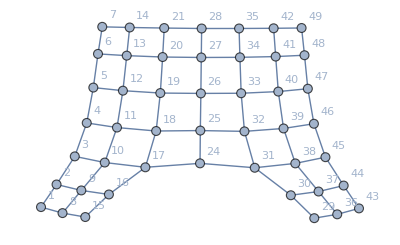

{1,2,3,10,17,24,31,30,29,36,43}

```mathematica
(* your code *)
FindShortestPath[Subscript[G, G], 1, 43]
Subscript[G, G] = VertexDelete[Subscript[G, G], {22, 23}]
FindShortestPath[Subscript[G, G], 1, 43]
```

svar:
(* Hva er korteste vei, angitt som en liste av noder, mellom node 1 og 43 før og etter at node 22 og 23 har feilet? *)
Før:
{1,8,15,22,29,36,43}

Etter:
{1,2,3,10,17,24,31,30,29,36,43}

(* Hvor mange og hvilke noder må minimum ha feilet for at veien mellom 1 og 20 er avbrutt? *)
Minimum to noder må feile. Dersom node 1 og 8 feiler er node 1 isolert. Kan og argumentere for at dersom node 1 eller 20 feiler, så er veien brutt.

### Oppgave I.3 Lag en funksjon som kombinerer flere stukturer til en graf med ulike strukturer

```mathematica
(* Funksjon for å kombinere ulike strukturer, bruker funksjoner for å danne linker mellom noder *)
Subscript[G, comb][E_:List,V_:List,opt_] := Graph[Flatten[E],Flatten[V],opt];

(*Funksjon for å danne ett-nivå stjernestruktur av nodene numerert mellomn(rot-node) ogm-nantall noder (inklusive rot-noden)*)
(* 
	s = connecting node;
	n = numbering from n;
	m = numbering to m;
*)
Subscript[FE, S][s_,n_,m_]:=Table[s<-> i,{i,n,m}];
```

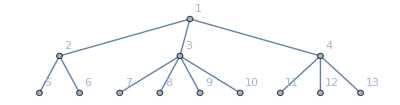

```mathematica
(* Eksempel 2: To-nivå stjernestruktur, 9 noder, bruk funksjon definert over *)
Subscript[G, comb][Table[i,{i,9}],{Subscript[FE, S][1,2,4],Subscript[FE, S][2,5,6],Subscript[FE, S][3,7,10],Subscript[FE, S][4,11,13]},VertexLabels->Table[i-> i,{i,13}]]
```

#### Kombinér grid-, ring-, og stjerne-topologi Plott kombinert graf

Et reelt nettdesign vil bestå av en kombinasjon av ulike strukturer.  
Sett sammen en graf bestående av 
i) Kjernenett med flere alternative veier: 9 noder i en 3x3 grid
ii) Metro/kant-nett med litt færre alternativer: 10 noder i ringstruktur - fire ringer som er tilkoplet til kjernenettet til fire ulike kjernenett-rutere
iii) Aksessnettet har få/ingen alternative: Buss- og/eller stjernenett struktur: tre stjernenett a 8 noder kooplet til hver sin kantruter i metronettet, samme for alle fire metronettene
Dette gir i alt 9 + 10*4 + 3*4*8 = 145 noder 

En slik struktur er typisk for konstruerte nett (som for eksempel Telenors IP-nett) med blant annet fornunftig balanse mellom pris og robusthet (bevisst valg redundans-nivå på ulike deler av nettet, kjerne, metro- og aksessnett).

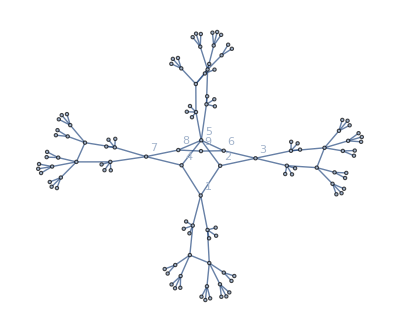

```mathematica
startab={};
cntab={1,3,5,7};
Do[nodes=10+k*28;
i=10+(k-1)*28;
cn=cntab[[k]];
startab = {startab,Subscript[FE, R][cn,i,i+3],
Subscript[FE, S][i,i+4,i+6], 
Subscript[FE, S][i+1,i+7,i+8],
Subscript[FE, S][i+2,i+14,i+16],
Subscript[FE, S][i+3,i+25,i+27],
Subscript[FE, S][i+7,i+9,i+11],
Subscript[FE, S][i+8,i+12,i+13],
Subscript[FE, S][i+14,i+17,i+19],
Subscript[FE, S][i+15,i+20,i+21],
Subscript[FE, S][i+16,i+22,i+24]},{k,1,4}];

nodes=121;
(* og nå lager vi nettverket Subscript[G, C] *)
Subscript[G, C]= Subscript[G, comb][Table[n,{n,nodes}],
{Subscript[FE, G][1,3,3],
(*Subscript[FE, R][cn,i,i+3],*)
startab},VertexLabels->Table[i-> i,{i,1,9}]
]
```

#### (a) Markér alle nodene i kjernenett med rødt

Hint: bruk HighlightGraph

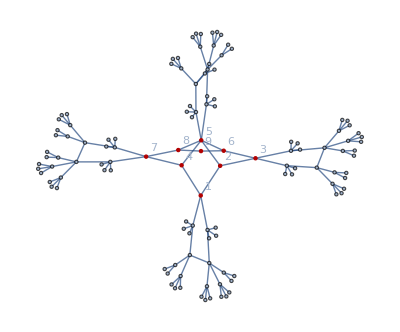

```mathematica
(* your code *)
HighlightGraph[Subscript[G, C], Range[1, 9]]
```

### Oppgave I.4 Lag random-grafer med 121 noder

Det finnes flere ulike metoder for å lage (tilfeldige) grafer for å studere ulike egenskaper til store topologier. 
Fordelen med å bruke “random graphs” er at det er mye enklere og mindre jobb enn å designe et nett basert på krav til sikkerhet og robusthet (og ytelse).

Felles for de ulike metodene er at de i liten, eller ingen, grad tar hensyn til geografiske/fysiske begrensinger.
Random-grafene blir derfor tilsynelatende (basert på visse kriterier) lik virkelige nett.  For fysiske, designede nett, er random-grafer ikke en god imitasjon, men for logiske, overlagrede, peer-to-peer nett og sosiale nett, er de svært illustrative. 

Vi skal her se nærmere på to random-grafer

#### BarabasiAlbertGraphDistribution

Barabasi-Albert (parameter k) 
	- starter med k_0=k noder
	- hver nye node som genereres linkes til k av de eksisterende nodene
	- den nye noden linkes tilfeldig til en node i, med sannsynlighet p_i= k_i/Σk_l , k_i er antall linker av node i og Σk_l er antall linker totalt i nettverket .08.08.08(dvs. dess flere linker en node har, dess større sannsynlighet for å få en ekstra link)
	 - dette danner en graf med et stort antall noder med få linker, og et lite antall noder med mange linker 
	 (sentrale linker, “super-nodes”, akkurat slik man finner i eet P2P-nett)

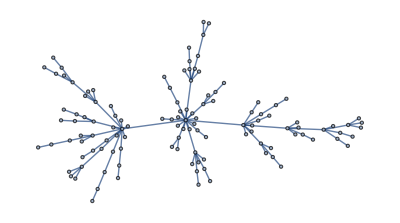

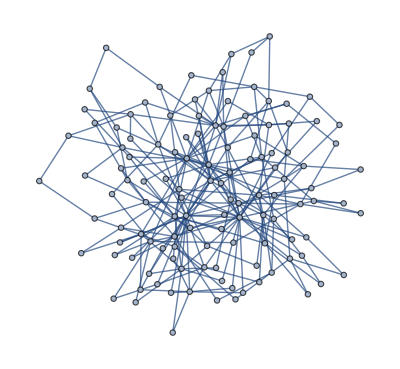

```mathematica
(* Barabasi-Albert med N=121,og k=1 og k=2 *) 
Subscript[G, BA1]=RandomGraph[BarabasiAlbertGraphDistribution[121,1]]
Subscript[G, BA2]=RandomGraph[BarabasiAlbertGraphDistribution[121,2]]
```

#### (a) Hva er korteste vei mellom node 100 og 121? Markér veien i grafen.

Hint: bruk HighlightGraph, PathGraph og FindShortestPath

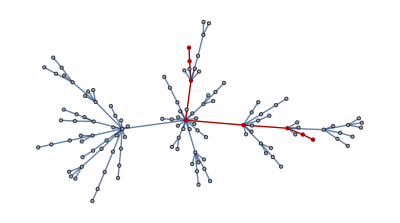

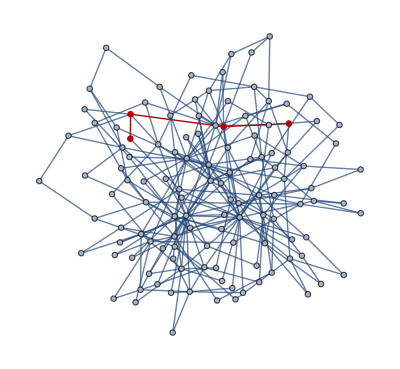

```mathematica
(* your code *)
HighlightGraph[Subscript[G, BA1], PathGraph[FindShortestPath[Subscript[G, BA1], 100, 121]]]
HighlightGraph[Subscript[G, BA2], PathGraph[FindShortestPath[Subscript[G, BA2], 100, 121]]]
```

#### WattsStrogatzGraphDistribution

Watts - Strogatz
	- start med N noder (det antall noder som nettet skal bestå av)
	- lag en ring hvor hver node i har K naboer, K/2 “upstreams” (i+1, i+2, osv) og K/2 “downstreams” 
	- med sannsynlighet p så endres linkene til node i fra e_(i,j) til e_(i,k), slik at, 
	k er uniformfordelt blant N noder, ekslusive node i og node j som allerede har en link fra node i. 
	- dette danner en graf hvor det er mer sannsynlig at en node er linket til sine naboer enn (a) {hvis p er liten}

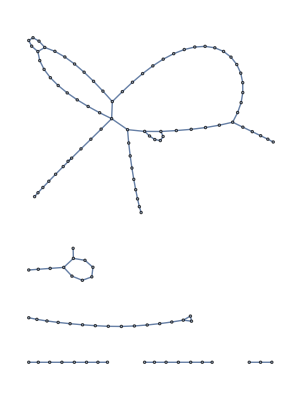

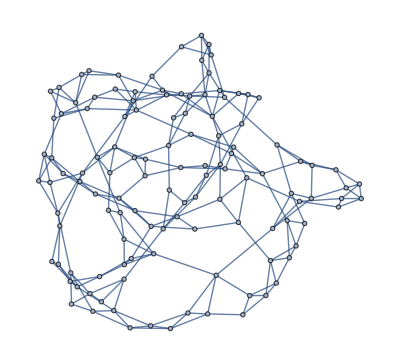

```mathematica
(* Watts-Strogatz med N=121, p=0.1 (k=1, default k=2) *) 
Subscript[G, WS1]=RandomGraph[WattsStrogatzGraphDistribution[121,0.1,1]]
Subscript[G, WS2]=RandomGraph[WattsStrogatzGraphDistribution[121,0.1]]
```

#### (a) Hva er korteste vei mellom node 100 og 121? Markér veien i grafen.

Hint: bruk HighlightGraph, PathGraph og FindShortestPath

-Graphics-

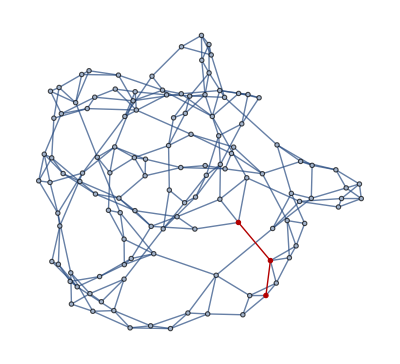

```mathematica
(* your code *)
HighlightGraph[Subscript[G, WS1], PathGraph[FindShortestPath[Subscript[G, WS1], 100, 121]]]
HighlightGraph[Subscript[G, WS2], PathGraph[FindShortestPath[Subscript[G, WS2], 100, 121]]]
```

## Del II: Strukuranalyse

### Oppgave II.1 Sammenlign de ulike grafene

#### (a) Hvor mange linker har hver topologi: G_C,G_BA1,G_BA2,G_WS1,G_WS2 (antall linker har stor kostnad)? Beregn gjennomsnittelig node degree.

```mathematica
(* your code *)
(* Subscript[G, C] *)
Edges: EdgeCount[Subscript[G, C]]
Average: Total[VertexDegree[Subscript[G, C]]] / VertexCount[Subscript[G, C]] // N

(* Subscript[G, BA1] *)
Edges: EdgeCount[Subscript[G, BA1]]
Average: Total[VertexDegree[Subscript[G, BA1]]] / VertexCount[Subscript[G, BA1]] // N

(* Subscript[G, BA2] *)
Edges: EdgeCount[Subscript[G, BA2]]
Average: Total[VertexDegree[Subscript[G, BA2]]] / VertexCount[Subscript[G, BA2]] // N

(* Subscript[G, WS1] *)
Edges: EdgeCount[Subscript[G, WS1]]
Average: Total[VertexDegree[Subscript[G, WS1]]] / VertexCount[Subscript[G, WS1]] // N

(* Subscript[G, WS2] *)
Edges: EdgeCount[Subscript[G, WS2]]
Average: Total[VertexDegree[Subscript[G, WS2]]] / VertexCount[Subscript[G, WS2]] // N
```

Edges:128

Average:2.1157

Edges:120

Average:1.98347

Edges:239

Average:3.95041

Edges:121

Average:2.

Edges:242

Average:4.

#### (b) Hva er Degree Distribution i topologiene G_C,G_BA1,G_BA2,G_WS1,G_WS2? (plot antall noder mot vertex degree/antall naboer)

Hint: se på “Noen nyttige mathematica-funksjoner” (funksjon “VertexDegree”)

2.1157

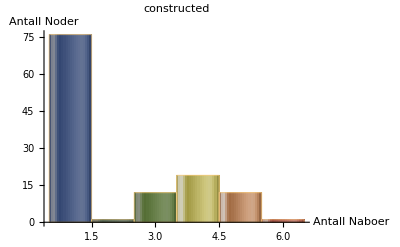

DegreeDistribuion:1.98347

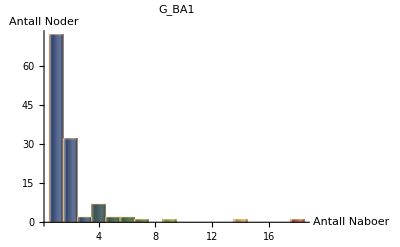

DegreeDistribuion:3.95041

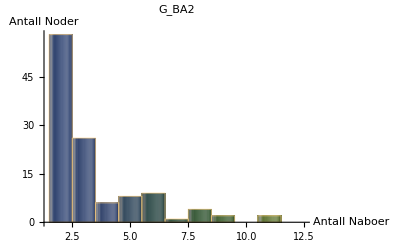

DegreeDistribuion:2.

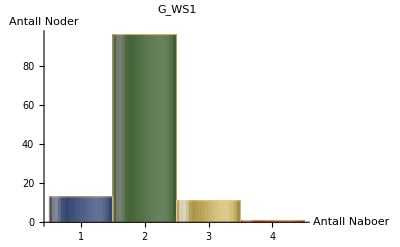

DegreeDistribuion:4.

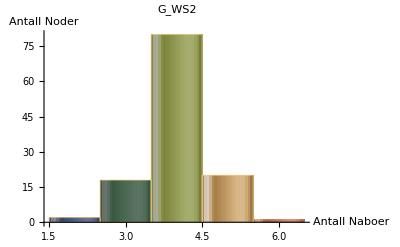

```mathematica
(* your code *)
(* Subscript[G, C] *)
DegreeDistribuion=
Total[VertexDegree[Subscript[G, C]] / VertexCount[Subscript[G, C]]] // N

Histogram[VertexDegree[Subscript[G, C]], 
20,
PlotLabel->"constructed",
AxesLabel->{"Antall Naboer","Antall Noder"},
ChartElementFunction->"GlassRectangle",
ChartStyle->"DarkRainbow"
]

(* Subscript[G, BA1] *)
DegreeDistribuion:
Total[VertexDegree[Subscript[G, BA1]] / VertexCount[Subscript[G, BA1]]] // N

Histogram[VertexDegree[Subscript[G, BA1]], 
20,
PlotLabel->"G_BA1",
AxesLabel->{"Antall Naboer","Antall Noder"},
ChartElementFunction->"GlassRectangle",
ChartStyle->"DarkRainbow"
]

(* Subscript[G, BA2] *)
DegreeDistribuion:
Total[VertexDegree[Subscript[G, BA2]] / VertexCount[Subscript[G, BA2]]] // N

Histogram[VertexDegree[Subscript[G, BA2]], 
20,
PlotLabel->"G_BA2",
AxesLabel->{"Antall Naboer","Antall Noder"},
ChartElementFunction->"GlassRectangle",
ChartStyle->"DarkRainbow"
]

(* Subscript[G, WS1] *)
DegreeDistribuion:
Total[VertexDegree[Subscript[G, WS1]] / VertexCount[Subscript[G, WS1]]] // N

Histogram[VertexDegree[Subscript[G, WS1]], 
20,
PlotLabel->"G_WS1",
AxesLabel->{"Antall Naboer","Antall Noder"},
ChartElementFunction->"GlassRectangle",
ChartStyle->"DarkRainbow"
]

(* Subscript[G, WS2] *)
DegreeDistribuion:
Total[VertexDegree[Subscript[G,WS2]] / VertexCount[Subscript[G, WS2]]] // N

Histogram[VertexDegree[Subscript[G, WS2]], 
20,
PlotLabel->"G_WS2",
AxesLabel->{"Antall Naboer","Antall Noder"},
ChartElementFunction->"GlassRectangle",
ChartStyle->"DarkRainbow"
]
```

Kommenter resultatene:
Constructed: 
Vi ser at nettverket har en del noder med få naboer, og en annen del med flere naboer. Delen der det er få naboer er en typisk access-del, - dette er da kantnodene. Ellers er fordelingen ganske nærme en normalfordeling, og dette utgjør kjernenettet. 

BA:
Har en typisk Power-law-fordeling. Man kan se av histogrammet at det verdiene er nærmest eksponentielt avtagende.  Det er forholdsvis mange noder med få naboer. De få nodene som har mange naboer er supernoder, og de har ansvar for mange kantnoder.

WS:
En overvekt av nodene har like mange naboer. Antallet naboer er ikke like spredt som i BA og Constructed. Normalfordelt.

#### (c) Hvordan forandrer Degree Distribution seg i et nettverk med BarabasiAlbertGraphDistribution når parameter k økes?

K er nærme gjennomsnittlig antallet kanter per node.
Når antallet kanter i grafen øker, så øker den totale degree distributionen seg. Dette er fordi hver node får flere kanter.

#### (d) Hvordan forandrer Degree Distribution seg i et nettverk med WattsStrogatzGraphDistribution når parametre forandres?

Når K øker, så øker det totale antallet kanter i grafen. Dette øker igjen den gjennomsnittlige vertex-degree’en.
Dersom vi øker P, så øker sannsynligheten for re-wiring. Dette gir oss en jevnere fordeling i grafen.

#### (e) Hva sier Degree Distribution om stabiliteten til et nettverk?

Hint: se på de forskjellige Degree Distributions, hvilket nettverk virker mest stabilt. Hvorfor?

Et nettverk består som oftest av en rekke noder. Et nettverk med mange noder med få linker er mindre stabilt enn et nettverk med mange noder med mange linker. Et ideelt nettverk har mange mange linker totalt og få noder med få linker. Av eksemplene over ser vi at både BA2 og WS2 ser stabile ut. Disse har en rekke noder med mer enn én nabo.. Problemet med å ha få kanter og mange noder, er at om én kant brytes, så er det mindre sannsynlig at det finnes en sammenhengende vei mello nodene, - nettverket splittes.

Dersom man har mange noder med mange linker, så vil det være høy ‘interconnectivity’ mellom nodene. Dette gjør at dersom én node feiler, er det likevel høy sannsynlighet for at det fortsatt finnes en kobling mellom nodene.

#### (f) Beregn de tre Centrality indeksene for G_C og G_WS1 . Prøv å finne noder som har en høy verdi i den ene indeksen men ikke i de andre. Hvor viktig er disse nodene (hva skjer når de feiler etc.)?

Du kan bruke koden her for å lage grafer. Du kan gjøre grafer større med å klikke på dem å trekke på rammen.
Node-størrelsen representerer centrality indeksen

```mathematica
centralityList={DegreeCentrality,BetweennessCentrality,ClosenessCentrality};
graphList={Subscript[G, C],Subscript[G, WS1]};
Table[HighlightGraph[g,VertexList[g],
VertexSize-> Thread[VertexList[g]-> Rescale[c[g]]]],{g,graphList},{c,centralityList}];
Grid[Prepend[%,centralityList]]

(* Values for Subscript[G, C] *)
"GC:"
DegreeC: DegreeCentrality[Subscript[G, C]]
BetweennessC: BetweennessCentrality[Subscript[G, C]]
ClosenessC: ClosenessCentrality[Subscript[G, C]]

"WS1:"
(* Values for Subscript[G, WS1] *)
DegreeC : DegreeCentrality[Subscript[G, WS1]]
BetweennessC: BetweennessCentrality[Subscript[G, WS1]]
ClosenessC: ClosenessCentrality[Subscript[G, WS1]]
```

DegreeCentrality | BetweennessCentrality | ClosenessCentrality
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

GC:

DegreeC:{4,3,4,3,6,3,4,3,2,5,4,5,5,1,1,1,4,3,1,1,1,1,1,4,3,4,1,1,1,1,1,1,1,1,1,1,1,5,4,5,5,1,1,1,4,3,1,1,1,1,1,4,3,4,1,1,1,1,1,1,1,1,1,1,1,5,4,5,5,1,1,1,4,3,1,1,1,1,1,4,3,4,1,1,1,1,1,1,1,1,1,1,1,5,4,5,5,1,1,1,4,3,1,1,1,1,1,4,3,4,1,1,1,1,1,1,1,1,1,1,1}

BetweennessC:{2752.,2175.,2607.33,2175.,3293.33,929.,2607.33,929.,160.,1098.,851.,1271.,1470.,0.,0.,0.,354.,237.,0.,0.,0.,0.,0.,354.,237.,354.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1098.,851.,1271.,1470.,0.,0.,0.,354.,237.,0.,0.,0.,0.,0.,354.,237.,354.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1098.,851.,1271.,1470.,0.,0.,0.,354.,237.,0.,0.,0.,0.,0.,354.,237.,354.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1098.,851.,1271.,1470.,0.,0.,0.,354.,237.,0.,0.,0.,0.,0.,354.,237.,354.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

ClosenessC:{0.228137,0.229446,0.206186,0.229446,0.230769,0.207254,0.206186,0.207254,0.188088,0.196399,0.174419,0.175439,0.197694,0.164384,0.164384,0.164384,0.149813,0.14944,0.130435,0.130435,0.130435,0.130152,0.130152,0.150565,0.150188,0.150565,0.131004,0.131004,0.131004,0.130719,0.130719,0.131004,0.131004,0.131004,0.165289,0.165289,0.165289,0.17991,0.16129,0.162162,0.180995,0.152672,0.152672,0.152672,0.140023,0.139697,0.122951,0.122951,0.122951,0.122699,0.122699,0.14068,0.140351,0.14068,0.123457,0.123457,0.123457,0.123203,0.123203,0.123457,0.123457,0.123457,0.153453,0.153453,0.153453,0.198347,0.175953,0.176991,0.199667,0.165746,0.165746,0.165746,0.150943,0.150565,0.131291,0.131291,0.131291,0.131004,0.131004,0.151707,0.151324,0.151707,0.131868,0.131868,0.131868,0.131579,0.131579,0.131868,0.131868,0.131868,0.166667,0.166667,0.166667,0.17991,0.16129,0.162162,0.180995,0.152672,0.152672,0.152672,0.140023,0.139697,0.122951,0.122951,0.122951,0.122699,0.122699,0.14068,0.140351,0.14068,0.123457,0.123457,0.123457,0.123203,0.123203,0.123457,0.123457,0.123457,0.153453,0.153453,0.153453}

WS1:

DegreeC:{4,2,2,2,3,1,2,2,2,2,2,2,2,2,1,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,2,2,2,1,2,2,2,2,3,3,2,2,2,2,2,2,3,1,2,2,2,2,2,2,2,3,3,3,2,2,2,2,1,2,2,1,2,1,3,2,2,2,2,2,3,1,2,2,2,2,1,2,2,2,2,2,1,2,2,2,2,2,1,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,1}

BetweennessC:{1684.93,650.,594.,536.,482.,0.,458.7,407.867,357.867,307.867,257.867,207.867,157.867,114.2,0.,74.,146.,216.,284.,677.267,346.767,298.767,250.767,202.767,160.333,139.567,148.233,175.067,209.067,246.233,284.233,322.233,360.233,400.733,446.233,494.233,542.233,590.233,0.,6.,10.,12.,12.,10.,6.,0.,92.2333,26.0667,5.83333,51.7667,171.433,299.467,336.133,386.133,436.133,486.133,536.133,586.133,1106.47,0.,74.,146.,216.,284.,350.,414.,476.,1355.77,998.1,879.1,761.767,723.767,685.767,647.767,0.,9.,16.,0.,1.,0.,26.,10.,6.,3.,4.,8.,18.,0.,89.,27.8333,10.8333,55.,0.,74.,146.,216.,284.,350.,0.,5.,8.,9.,8.,5.,0.,0.,0.,26.,36.,44.,50.,54.,56.,56.,54.,50.,44.,36.,26.,14.,0.}

ClosenessC:{0.152749,0.137615,0.124792,0.113809,0.104312,0.0945776,0.137615,0.12605,0.116279,0.107914,0.100671,0.0943396,0.0887574,0.0837989,0.0676285,0.0724638,0.0778816,0.0839866,0.0909091,0.0988142,0.0929368,0.0877193,0.0830565,0.0788644,0.0750751,0.0733138,0.074331,0.0766088,0.0793651,0.0826902,0.0863061,0.0902527,0.0945776,0.0993377,0.106082,0.113809,0.12275,0.133215,0.25,0.318182,0.388889,0.4375,0.4375,0.388889,0.318182,0.25,0.0802139,0.0746269,0.0708215,0.0758342,0.0816104,0.0867052,0.0920245,0.0980392,0.104895,0.112782,0.121951,0.132743,0.145631,0.0720461,0.0775595,0.0837989,0.0909091,0.0990753,0.108538,0.119617,0.132743,0.148515,0.140187,0.13181,0.123558,0.116279,0.10981,0.104022,0.243902,0.3125,0.4,0.666667,1.,0.666667,0.5,0.416667,0.357143,0.322581,0.333333,0.384615,0.454545,0.322581,0.123967,0.111111,0.105783,0.117371,0.0661959,0.0708215,0.0759878,0.0817884,0.0883392,0.0957854,0.285714,0.375,0.461538,0.5,0.461538,0.375,0.285714,0.141509,0.141509,0.16129,0.180723,0.2,0.217391,0.230769,0.238095,0.238095,0.230769,0.217391,0.2,0.180723,0.16129,0.142857,0.12605}

Svar:
G_C :
Vi ser her at nodene i kjernenettet har skyhøy betweenness centrality. Dette betyr at det passerer mye trafikk her, og dersom en av disse nodene feiler kan det ramme trafikken i nettverket. Vi ser at de nodene som har høy betweenness centrality også har høy closeness centrality. Det vil si at selv om de feiler er det ikke nødvendigvis krise, da det er mange andre noder i relativ nærhet.  

G_WS1 : 
Nodene har gjennomsnittlig degree centrality og closeness centrality. Vi ser dog at i midten er det en lengre rekke av noder med høy betweenness. Dersom en av disse brytes har det store konsekvenser for nettverket. En feil her vil ramme veiene store deler av trafikken tar. De nodene som har lav betweenness er trolig de i den nedre ‘sub-grafen’, - disse er helt adskilt fra den øvre ‘sub-grafen’, og vil ikke ha noen mulighet til å kobles til de andre.  Mange av nodene ligger på rekke, og noden i midten vil ha den høyeste closeness-centrality’en.

#### (g) Lag en graf med 10-20 noder som har en node med høy closeness centrality men lav degree centrality

Noden skal ha høyeste closeness centrality verdi men en vanlig (ikke høyest) degree centrality.

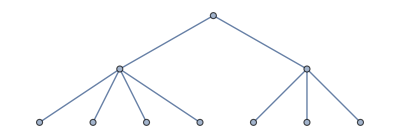

```mathematica
(* your code *)
graf=Graph[Range[1, 10],{1<->2,2<->3,2<->4,2<->5,2<->6,7<->1,7<->8,7<->9,7<->10}]
```

```mathematica
(* Use this function to compute the centrality indices in your graph *)
centralityList={DegreeCentrality,ClosenessCentrality};
Table[HighlightGraph[g,VertexList[g],
VertexSize-> Thread[VertexList[g]-> Rescale[c[g]]],VertexLabels->Thread[VertexList[g]->c[g]]
],

{g,{graf}},
{c,centralityList}];
Grid[Prepend[%,centralityList]]
```

DegreeCentrality | ClosenessCentrality
-Graphics- | -Graphics-

### Oppgave II.2 Analyser reelle nettverk

På http://www.topology-zoo.org/dataset.html finner du flere topologier av IKT nettverk. Når du har lastet dem ned (graphml format) så kan du importere dem med:

```mathematica
uninett=Import["/etstedpådindisk/Uninett2011.graphml"];
Graph[uninett,ImageSize->{1000,700}];
```

Import::nffil: File /etstedpådindisk/Uninett2011.graphml not found during Import.

Importer 3 forskjellige nettverk og plot Degree Distribution. Kommenter hva du ser. Hvilket av de nettene ovenfor ligner de mest på?

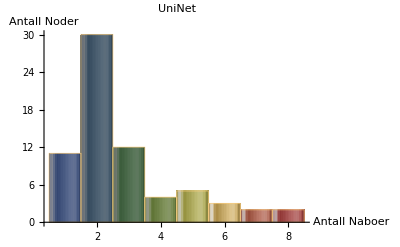

-Graphics-

```mathematica
(* netverk 1 *)
uninet=Import["/Users/magnusholtet/Development/Github/NTNU/TTM4185 - Sikkerhet og robusthet i IKT-system/uniNet.graphml"];
Graph[uninet,ImageSize->{1000,700}];
Histogram[VertexDegree[uninet],
PlotLabel->"UniNet",
AxesLabel->{"Antall Naboer","Antall Noder"},
ChartElementFunction->"GlassRectangle",
ChartStyle->"DarkRainbow"
]
```

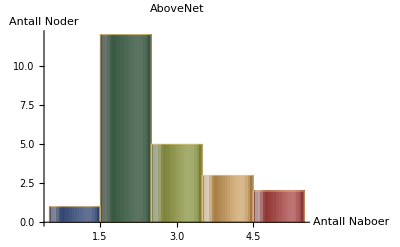

```mathematica
(* netverk 2 *)
abovenet=Import["/Users/magnusholtet/Development/Github/NTNU/TTM4185 - Sikkerhet og robusthet i IKT-system/aboveNet.graphml"];
Graph[abovenet,ImageSize->{1000,700}];
Histogram[VertexDegree[abovenet],
PlotLabel->"AboveNet",
AxesLabel->{"Antall Naboer","Antall Noder"},
ChartElementFunction->"GlassRectangle",
ChartStyle->"DarkRainbow"
]
```

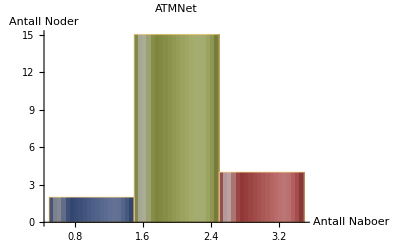

```mathematica
(* netverk 3 *)
atmnet=Import["/Users/magnusholtet/Development/Github/NTNU/TTM4185 - Sikkerhet og robusthet i IKT-system/atmNet.graphml"];
Graph[atmnet,ImageSize->{1000,700}];
Histogram[VertexDegree[atmnet],
PlotLabel->"ATMNet",
AxesLabel->{"Antall Naboer","Antall Noder"},
ChartElementFunction->"GlassRectangle",
ChartStyle->"DarkRainbow"
]
```

Kommentar/Diskusjon:
Alle degree distributionene ligner forholdsvis mye på Watts Strogatz distribusjonen. Det er tenkelig at det har vært en Watts Strogatz distribusjon med K lik 1, da snittet i alle distribusjonene er rundt 2.

Det er ikek mulig å ha færre kanter enn 0, og da snittet ligger på to, så er det naturlig at normalfordelingen heller mot høyre (Hver node har flere kanter), men i alle tre tilfellene er det svært få supernoder.

## DEL III: Feil og angrep på nett

### Oppgave III.1 Tilfeldige feil - antall noder i største partisjon

#### (a) Lag en modul som fjerner tilfeldig 5-120 (i steg av 5) linker fra en graf og gir tilbake antall noder i den største partisjon etter at linkene er fjernet fra grafen. Test modulen med graphen G_C;

Hint: antall partisjoner finnes ved bruk av funksjonen: “ConnectedComponents[graf]”, og antall noder i den største partisjonen finnes ved bruk av “Length[ConnectedComponents[graf][[1]]]” siden den største partisjonen alltid er det første elementet i listen.

```mathematica
(* Module to compute remaining  *)

(* Delete edge *)

tilfeldigeFeil[Graf_] := Module[
(*
input: en graf ;
output: en liste "tab" som inneholder elementer:{<antall slettede noder>,<antall noder i største komponent i %>}
*)

{tab,survivingNodes,components,NE,DG,max},
DG=Graf;
max=VertexCount[DG];
tab={{0,max}};
Do[
(* Parameters *)
NE:=RandomSample[EdgeList[DG],5];
DG=EdgeDelete[DG,NE];

(* Check partitions *)
components = ConnectedComponents[DG];
(* Select first element, which is the largest one *) 
survivingNodes=(components[[1]] //Length);

tab=Append[tab,{XX,survivingNodes}]; (* add new datapoint to list *)
,{XX,5,120,5}
];
(*CP=ListPlot[tab, Joined->True];*)
Return[tab]
(*Return[ListPlot[tab,Joined->True,PlotStyle->style,AxesLabel->{"# deleted vertices","Surviving vertices"}] ];*)
];
```

Test modulen med å kjøre dette her:

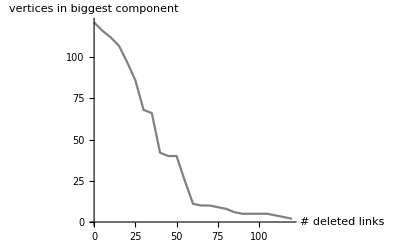

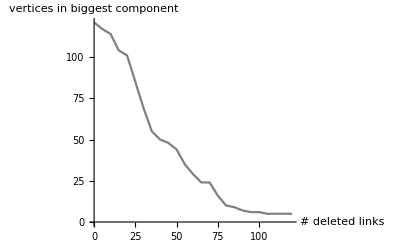

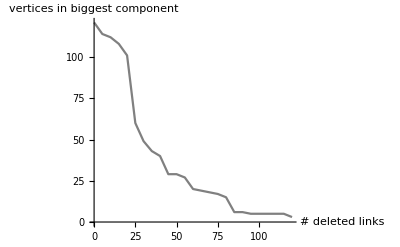

```mathematica
ListLinePlot[tilfeldigeFeil[Subscript[G, C]],PlotStyle->Gray,AxesLabel->{"# deleted links","vertices in biggest component"}]
ListLinePlot[tilfeldigeFeil[Subscript[G, C]],PlotStyle->Gray,AxesLabel->{"# deleted links","vertices in biggest component"}]
ListLinePlot[tilfeldigeFeil[Subscript[G, C]],PlotStyle->Gray,AxesLabel->{"# deleted links","vertices in biggest component"}]
```

Hvorfor får du tre forskjellige grapher?

Svar:
Funksjonen tilfeldigeFeil[...] kalles tre ganger. Siden det er tilfeldige linker som feiler, er det naturlig at det er tre ulike grafer.

#### (b) simulate: Bruk modulen tilfeldigeFeil på nettverk G_C,G_BA1,G_BA2,G_WS1,G_WS2. Repeter R=100 ganger (replikasjoner) og beregn gjenomsnittverdi for hver nettverk.

Hint: Repetisjoner kan implementeres ved bruk av Table[...,{repetitions}]

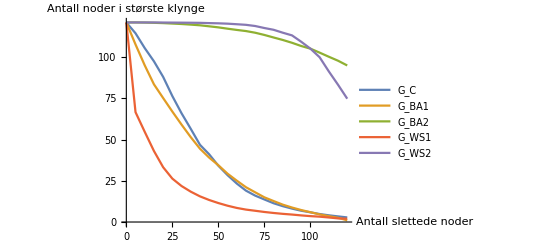

```mathematica
(* your code *)
values := {
Mean[Table[tilfeldigeFeil[Subscript[G, C]], {100}]],
Mean[Table[tilfeldigeFeil[Subscript[G, BA1]], {100}]],
Mean[Table[tilfeldigeFeil[Subscript[G, BA2]], {100}]],
Mean[Table[tilfeldigeFeil[Subscript[G, WS1]], {100}]],
Mean[Table[tilfeldigeFeil[Subscript[G, WS2]], {100}]]
}

ListLinePlot[values, 
PlotLegends->{"G_C", "G_BA1", "G_BA2", "G_WS1", "G_WS2"},
AxesLabel->{"Antall slettede noder", "Antall noder i største klynge"}
]
```

#### (b*) Plott det samme, men legg til errorbars for hvert punkt for å angi usikkerheten til hvert punkt

[valgfri] 
	(bruk ErrorListPlot som trenger pakken “ErrorBarPlots”, importered ved Needs[“ErrorBarPlots`”])

```mathematica
(* MED ERRORBARS *)

(* bruk ErrorListPlot som trenger pakken "ErrorBarPlots"*)
Needs["ErrorBarPlots`"];

(* Delete edge *)
(* Module for plotting *)
(* do R_ repetitions*)
plot[Graf_,R_,style_:Blue] := Module[
{tab={},
errortab={}},
Do[
(* Parameters *)
X=0;
X2=0;
EL=EdgeList[Graf];
(*EL=VertexList[Graf];*)
(*NE:= EL[[RandomSample[Range[Length[EL]],nedge]]];*)
NE:=RandomSample[EdgeList[Graf],XX];

(* Loop - simulate - estimate *)
Do[DG=EdgeDelete[Graf,NE];
(*DG=VertexDelete[Graf,NE];*)
(* Check partitions *)
sett = ConnectedComponents[DG];
(* Select first element, which is the largest one *) 
YY=(sett[[1]] //Length);
(* Sufficient observators for estimation of mean and standard error *)
X = X + YY;
X2 = X2 + YY^2;,
{R}];

mean=X/R ;
sterr=Sqrt[X2/(R-1)-R/(R-1)(X/R)^2];
tab=Append[tab,{XX,X/R}];

errortab = Append[errortab,{{XX,mean},ErrorBar[sterr]}];
,{XX,5,120,5}
];
(*CP=ListPlot[tab, Joined->True];*)
Return[ErrorListPlot[errortab,Joined->True,PlotStyle->style,AxesLabel->{"# deleted links","Surviving vertices"}] ];
];
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
(* Plot for engineered topologi (grafSubscript[G, C])-bruk ListPlot *)
Subscript[CP, C]=plot[Subscript[G, C],100, Gray];
(* Plot random topologi : Barabasi-Albert - k=1 *)
Subscript[CP, BA1]=plot[Subscript[G, BA1],100, Blue];
(* Plot random topologi : Barabasi-Albert - k=2 *)
Subscript[CP, BA2]=plot[Subscript[G, BA2],100, {Dotted, Blue}];
(* Plot random topologi : Watts-Strogatz - k=1 *)
Subscript[CP, WS1]=plot[Subscript[G, WS1],100, Brown];
(* Plot random topologi : Watts-Strogatz - k=2 *)
Subscript[CP, WS2]=plot[Subscript[G, WS2],100,  {Dotted, Brown}];
```

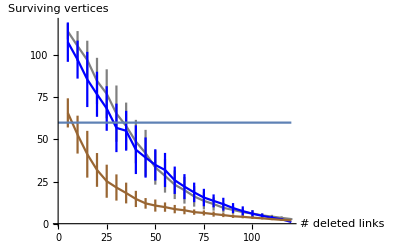

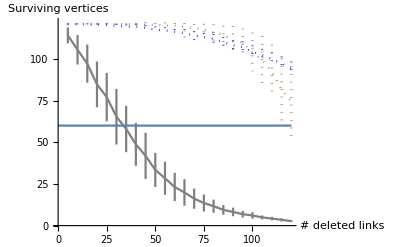

```mathematica
CT = ListPlot[{{0,60},{120,60}},Joined->True];
Show[Subscript[CP, C],Subscript[CP, BA1],Subscript[CP, WS1],CT,PlotRange->All]
Show[Subscript[CP, C],Subscript[CP, BA2],Subscript[CP, WS2],CT,PlotRange->All]
```

#### (c) Sammenlign de tre topologiene og kommenter egenskaper vs kostnad ved realisering

Hint: bruk resultat fra Del II

Svar:
Det er stor forskjell på grafene, og vi ser det er et ganske tydelig skille på grafene som ligger lavt vs. de som ligger høyt. 
Grafene som er generert med en høyere K-verdi er mer robuste (og dyrere) da det er flere linker totalt i nettverket. Grafene med K = 2 har langt flere linker, og er dermed langt mer ‘interconnected’, og dette resutlerer i en høyere robusthet. Dette nettopp fordi hver node er koblet til mange nadre noder.

#### (d) Vi har her brukt antall noder i største partisjon som pålitelighetsmål. Diskuter fordeler og ulemper med dette målet.

Hint: Hva sier tallene om pålitelighet i et realt netverk?

Svar:
Det er dessverre flere ulemper enn fordeler med å bruke dette pålitelighetsmålet. En klar fordel med dette målet er at det er enkelt å fremstille og beregne. Det er dog mer problematisk at man tilegner nodene samme verdi i denne fremstillingen. Det er på ingen måte gitt at hver enkelt node har samme verdi, - en node kan feks være koblet til en enkelt nabonode, mens en annen er koblet til et informasjonssenter eller noe annet av høy verdi. I tillegg ser vi kun på den største partisjonen, og ut i fra den kan vi ikke si noe om resten av nettverket og status der.

### Oppgave III.2 Målrettet angrep: hva vil du fjerne (tenk både på noder og linker).

#### (a) Lag en modul, simulate og plot resultater

Gjør det samme som før, men nå er det ikke lenger en tilfeldig feil men en målrettet angrep som prøver å skade nettverk så sterk som mulig. 
Skriv en modul som fjerner stegvis alle noder etter to forskjellige strategier: 
1) fjern de nodene med flest linker (DegreeCentrality-verdi)
2) fjern de nodene med høyest ClosenessCentrality-verdi
3) fjern de nodene med høyest BetweennessCentrality-verdi
Plot antall noder i største partisjonen mot antall fjernete noder.
Gjør det med alle nettverk G_C,G_BA1,G_BA2,G_WS1,G_WS2

```mathematica
(* Function to plot number of connected nodes (in largest partition) with targetted removing of node, strategy can be chosen by "method"*)
attackplot[Graf_,nnodes_,max_,method_,style_]:=
Module[{sgraf,tab = {{0,1}}},
sgraf = Graf;
Do[
If[VertexCount[sgraf]==0,Break[]]; (*stop if no nodes left*)
Bpart=ConnectedComponents[sgraf][[1]]; (* take biggest component *)
tab =Append[tab,{x,Length[Bpart]/nnodes}]; (* add new data point to list *)
sgraf=Subgraph[sgraf,Bpart]; (*take biggest component graph*)
vtab=method[sgraf]; (* use specified method to assign number to vertices *)
pos=Position[vtab,Max[vtab]][[1]][[1]]; (* take most vulnerable vertex *)
del = Bpart[[pos]]; (* get the vertex to delete *)
(*If[Length[del]>0,*)sgraf=VertexDelete[sgraf,del];(* delete one vertex *)
,{x,1,max}
];
Return[
ListPlot[tab,
Joined->True,
PlotStyle->style,
PlotRange->{All,{0,1}},
PlotLabel->"Attack Plot",AxesLabel->{"# deleted vertices","Surviving vertices [%]"}
]
];
];
```

Plot resultater for de forskjellige metoder og alle nettverk.

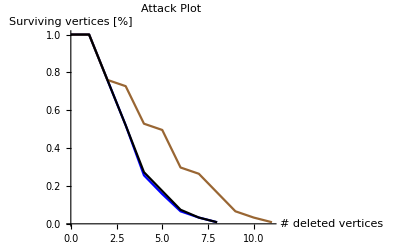

```mathematica
(* Different attacks; designed network *)
maxdelete=20;
Subscript[CDTP, C]=attackplot[Subscript[G, C],121,maxdelete,ClosenessCentrality,Blue];
Subscript[DDTP, C]=attackplot[Subscript[G, C],121,maxdelete,DegreeCentrality,Brown];
Subscript[BDTP, C]=attackplot[Subscript[G, C],121,maxdelete,BetweennessCentrality,Black];
Show[Subscript[CDTP, C],Subscript[DDTP, C],Subscript[BDTP, C], PlotRange->All]
```

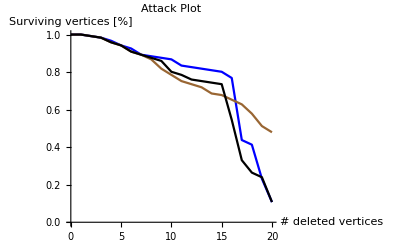

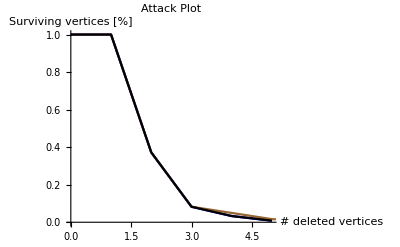

```mathematica
(* Different attacks; B-A, k=2 *)
maxdelete=20;
Subscript[CDTP, BA2]=attackplot[Subscript[G, BA2],121,maxdelete,ClosenessCentrality,Blue];
Subscript[DDTP, BA2]=attackplot[Subscript[G, BA2],121,maxdelete,DegreeCentrality,Brown];
Subscript[BDTP, BA2]=attackplot[Subscript[G, BA2],121,maxdelete,BetweennessCentrality,Black];
Show[Subscript[CDTP, BA2],Subscript[DDTP, BA2],Subscript[BDTP, BA2]]

(* Different attacks; B-A, k=1 *)
Subscript[CDTP, BA1]=attackplot[Subscript[G, BA1],121,maxdelete,ClosenessCentrality,Blue];
Subscript[DDTP, BA1]=attackplot[Subscript[G, BA1],121,maxdelete,DegreeCentrality,Brown];
Subscript[BDTP, BA1]=attackplot[Subscript[G, BA1],121,maxdelete,BetweennessCentrality,Black];
Show[Subscript[CDTP, BA1],Subscript[DDTP, BA1],Subscript[BDTP, BA1]]
```

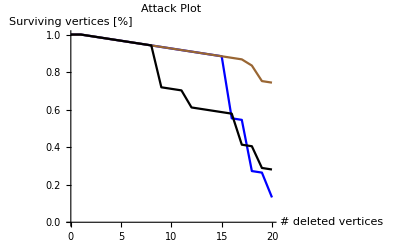

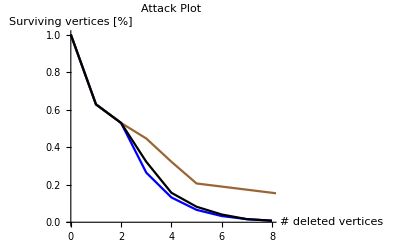

```mathematica
(* Different attacks; W-S, k=2 *)
maxdelete=20;
Subscript[CDTP, WS2]=attackplot[Subscript[G, WS2],121,maxdelete,ClosenessCentrality,Blue];
Subscript[DDTP, WS2]=attackplot[Subscript[G, WS2],121,maxdelete,DegreeCentrality,Brown];
Subscript[BDTP, WS2]=attackplot[Subscript[G, WS2],121,maxdelete,BetweennessCentrality,Black];

Show[Subscript[CDTP, WS2],Subscript[DDTP, WS2],Subscript[BDTP, WS2]]
(* Different attacks; W-S, k=1 *)
Subscript[CDTP, WS1]=attackplot[Subscript[G, WS1],121,maxdelete,ClosenessCentrality,Blue];
Subscript[DDTP, WS1]=attackplot[Subscript[G, WS1],121,maxdelete,DegreeCentrality,Brown];
Subscript[BDTP, WS1]=attackplot[Subscript[G, WS1],121,maxdelete,BetweennessCentrality,Black];
Show[Subscript[CDTP, WS1],Subscript[DDTP, WS1],Subscript[BDTP, WS1]]
```

Er det en forskjell mellom de ulike angreps strategier/metoder? Er det en som er best/skader nettverk mest? Hvis ja, hvorfor?

Kommentar/Diskusjon:
Closeness og betweenness skader nettverket i stor grad like mye over samme tidsrom. Det som derimot skader nettverket mest, er om man fjerner de nodene som har høyest DegreeCentrality. Det er tilfelle, fordi dersom man tar de nodene med flest linker, så er sannsynligheten for at en node ‘dør’ mye høyere.

#### (b) Sammenlign topologier

Plot resultater for de forskjellige topologier sammen og forklar hva du ser.

Hint: du kan kombinere flere plots med Show[plot1, plot2, ...]

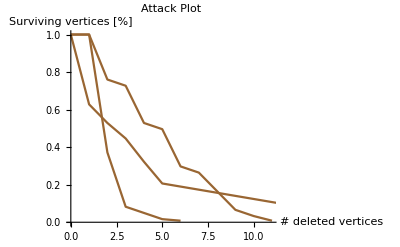

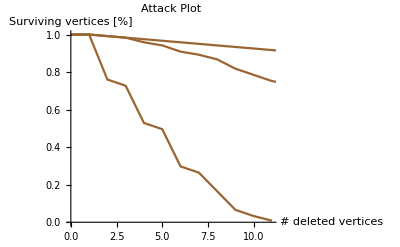

```mathematica
(* Designed vs. random graphs with the same number of links *)
Show[Subscript[DDTP, C],Subscript[DDTP, BA1],Subscript[DDTP, WS1]]
(* Designed vs. random graphs with double number of links *)
Show[Subscript[DDTP, C],Subscript[DDTP, BA2],Subscript[DDTP, WS2]]
```

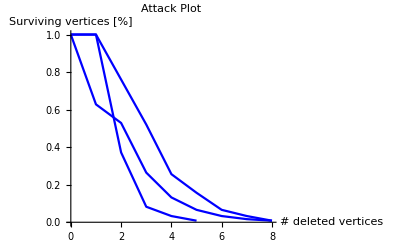

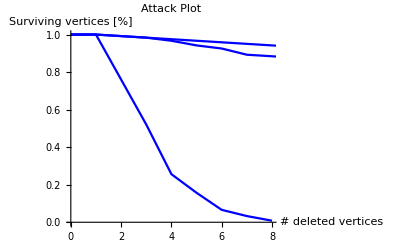

```mathematica
(* Designed vs. random graphs with the same number of links *)
Show[Subscript[CDTP, C],Subscript[CDTP, BA1],Subscript[CDTP, WS1]]
(* Designed vs. random graphs with double number of links *)
Show[Subscript[CDTP, C],Subscript[CDTP, BA2],Subscript[CDTP, WS2]]
```

Er det en forskjell mellom de ulike nettverkene? Er det et som er mest sårbart? Hvis ja, hvorfor?

Kommentar/Diskusjon:
Det er liten forskjell mellom de tre nettverkene når vi angriper, dersom k er 1. Om k er 2 derimot, ser vi at grafen C sliter.
Angrep som fokuserer på noder som har høy ClosenessCentrality gjør det best.

#### (c) simulate

For nettverket G_BA2, simuler de tre ulike angrepsberegningene med maxdelete=20 og R=20 ganger (replikasjoner). Beregn gjennomsnittsverdi og plot grafen.

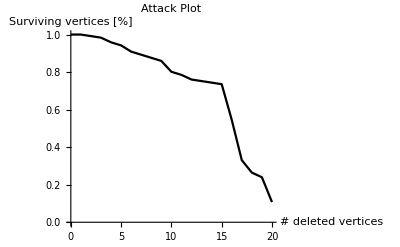

-Graphics-

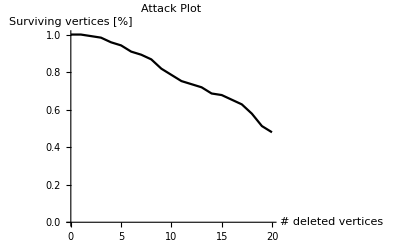

-Graphics-

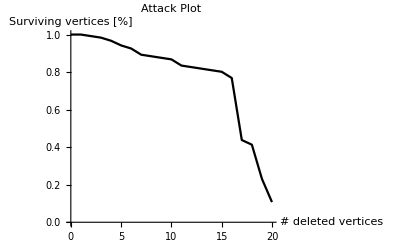

-Graphics-

```mathematica
(* your code *)
(* 20 kjøringer av BetweennessCentrality *)
Mean[
Table[
attackplot[Subscript[G, BA2], 121,maxdelete,BetweennessCentrality,Black],
20]
]

(* 1 kjøring *)
attackplot[
Subscript[G, BA2],
121,maxdelete,BetweennessCentrality,Black
]

(* 20 kjøringer av DegreeCentrality *)
Mean[
Table[
attackplot[Subscript[G, BA2], 121,maxdelete,DegreeCentrality,Black],
20]
]

(* 1 kjøring *)
attackplot[
Subscript[G, BA2],
121,maxdelete,DegreeCentrality,Black
]

(* 20 kjøringer av ClosenessCentrality*)
Mean[
Table[
attackplot[Subscript[G, BA2], 121,maxdelete,ClosenessCentrality,Black],
20]
]

(* 1 kjøring *)
attackplot[
Subscript[G, BA2],
121,maxdelete,ClosenessCentrality,Black
]
```

Sammenlign resultat med hva du får med kun en repetisjon:

Kommentar/Diskusjon:
Det utgjør ingen forskjell å kjøre funksjonen 20 ganger vs. 1 gang. Snittet er identisk, og det vil være hensiktsmessig å kun kjøre én gang.

### Oppgave III.3 Sammenlign egenskapene

#### (a) Sammenlign egenskapene til de ulike topologiene med hensyn på toleranse av tilfeldige feil og målrettede angrep

Lag en plot som inneholder resultat fra tilfeldige feil og resultater fra målrettede angrep (alt ble beregnet før). Lag en plot for hver topologi. Kommenter hva du ser (er det en forskjell? etc.) 

For å plotte tilfeldige feil og målrettede angrep i samme plot må du skrive om en funksjon for å få samme y-akse. Hint: Du kan bruke ListLinePlot til å skrive om plottet med tilfeldige feil.

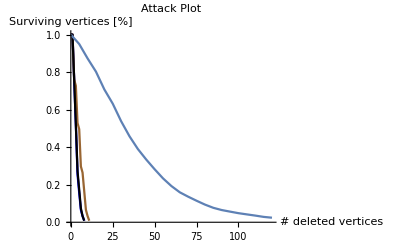

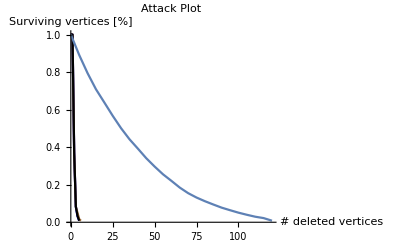

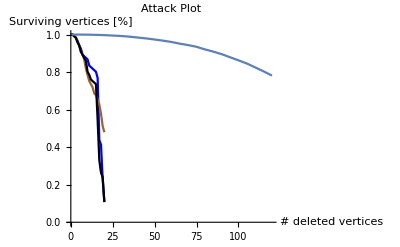

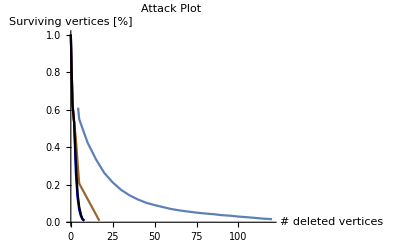

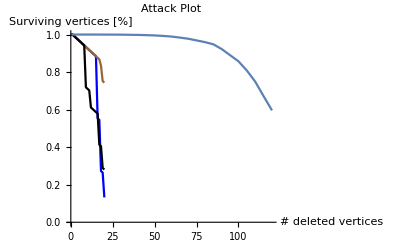

```mathematica
(* your code *)
(* Beregn snitt og del y-verdi på 121 for å konvertere til prosent *)
Subscript[RG,C]:=ListLinePlot[{#[[1]],#[[2]]/121}&/@Mean[Table[tilfeldigeFeil[Subscript[G,C]],{100}]]]
Show[Subscript[CDTP,C],Subscript[DDTP,C],Subscript[BDTP,C],Subscript[RG,C],PlotRange->{{0,120},{0,1}}]

Subscript[RG,BA1]:=ListLinePlot[{#[[1]],#[[2]]/121}&/@Mean[Table[tilfeldigeFeil[Subscript[G,BA1]],{100}]]]
Show[Subscript[CDTP,BA1],Subscript[DDTP,BA1],Subscript[BDTP,BA1],Subscript[RG,BA1],PlotRange->{{0,120},{0,1}}]

Subscript[RG,BA2]:=ListLinePlot[{#[[1]],#[[2]]/121}&/@Mean[Table[tilfeldigeFeil[Subscript[G,BA2]],{100}]]]
Show[Subscript[CDTP,BA2],Subscript[DDTP,BA2],Subscript[BDTP,BA2],Subscript[RG,BA2],PlotRange->{{0,120},{0,1}}]

Subscript[RG,WS1]:=ListLinePlot[{#[[1]],#[[2]]/121}&/@Mean[Table[tilfeldigeFeil[Subscript[G,WS1]],{100}]]]
Show[Subscript[CDTP,WS1],Subscript[DDTP,WS1],Subscript[BDTP,WS1],Subscript[RG,WS1],PlotRange->{{0,120},{0,1}}]

Subscript[RG,WS2]:=ListLinePlot[{#[[1]],#[[2]]/121}&/@Mean[Table[tilfeldigeFeil[Subscript[G,WS2]],{100}]]]
Show[Subscript[CDTP,WS2],Subscript[DDTP,WS2],Subscript[BDTP,WS2],Subscript[RG,WS2],PlotRange->{{0,120},{0,1}}]
```

Kommentar/Diskusjon:
Av grafene ser vi at målrettede angrep rammer mye hardere enn tilfeldige feil.

BS2 og WS2 er meget robuste sammenlignet med de andre grafene. Dette skyldes at disse nettverkene har langt flere linker. De målrettede angrepene har til hensikt å ramme nodene selv, mens de tilfeldige angrepene har til hensikt å ramme kantene. Dette resulterer i at node-angrep også rammer linker, da alle nodene er minimum tilkoblet én link.